# Whale Population Simulation

The  blue  whale  and  fin  whale  are  two  similar  species  that  inhabit  the  same  areas . Hence  they  are  thought  to  compete . The  intrinsic  growth  rate  of  each  species  is  estimated  at  5 %  per  year  for  the  blue  whale  and  8 %  per  year  for  the  fin  whale . The  environmental  carrying  capacity  (the  maximum  number  of  whales  that  the  environment  can  support)  is  estimated  at  150,000  blue  whales  and  400,000  fin  whales . The  extent  to  which  the  whales  compete  is  unknown . In  the  last  100  years  intense  harvesting  has  reduced  the  whale  population  to  around  3000  blues  and  15000  fins . Firstly, we  will  create  a  mathematical  model  representing  the  population  of  whales . Using  the  mathematical  model, we  will  determine  if  both  species  of  whales  grow  back, or  will  one  or  both  become  extinct.

We will model the problem as a dynamical system, with the population of each whale species representing a state variable.
B = number of blue whales
F = number of fin whales
gB = growth rate for blue whales (per year)
gF = growth rate for fin whales (per year)
cB = effect of competition on blue whales (whales per year) cF = effect of competition on fin whales (whales per year)

Assumptions:
gB =0.05B(1−B/150,000)
gF =0.08F(1−F/400,000)
cB = cF = αBF,
B ≥ 0, F ≥ 0, α > 0

We can now build the model using the assumptions. The populations B and F are functions of the independent variable t. 
dBdt[B_, F_] := 0.05*B*((B - 3000)/(B + 3000))*(1 - B/150000) - 10^-8*B*F
dFdt[B_, F_] := 0.08*F*((F - 15000)/(F + 15000))*(1 - F/400000) - 10^-8*B*F

Using  a  computer  implementation  of  Euler’ s  Method  we  will  simulate  the  behaviour  of  the  model  starting  with  initial  conditions  𝐵 (0) = 5, 000  and  𝐹 (0) = 70, 000.  Perform  a  sensitivity  analysis  on  both  𝑇  and  𝑁  to  ensure  the  validity  of  your  results , and determine if  both  species  of  whales  grow  back, or  one  or  both  will become  extinct, and about  how  long  it will  take.

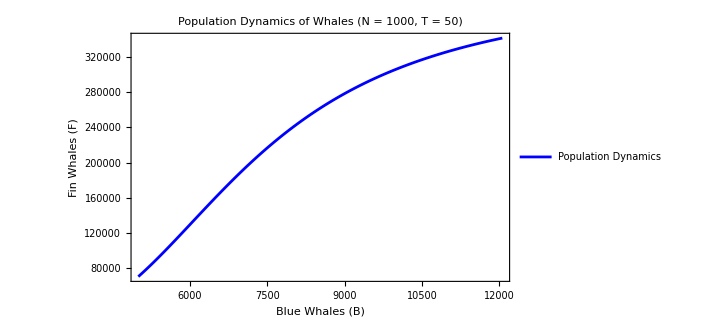
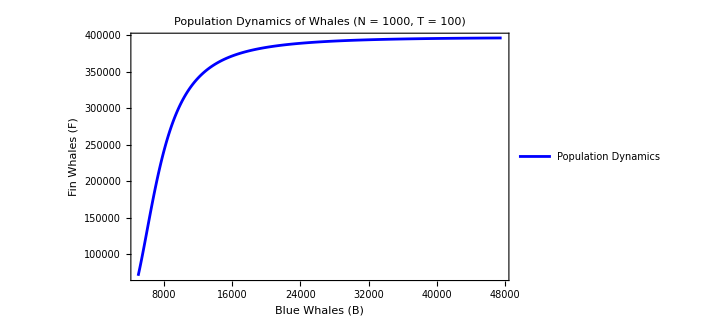
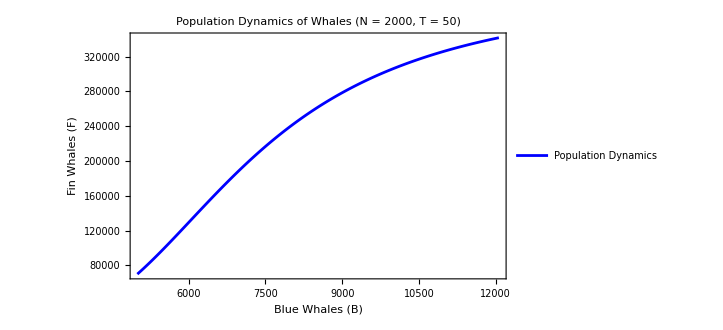

```mathematica
(* Define the system of differential equations *)
dBdt[B_, F_] := 0.05*B*((B - 3000)/(B + 3000))*(1 - B/150000) - 10^-8*B*F
dFdt[B_, F_] := 0.08*F*((F - 15000)/(F + 15000))*(1 - F/400000) - 10^-8*B*F

(* Implement Euler's method *)
eulerMethod[{B0_, F0_}, T_, numSteps_] := Module[{h, tValues, BValues, FValues, dB, dF, B, F},
  h = T/numSteps;
  tValues = Table[t, {t, 0, T, h}];
  BValues = FValues = Table[0, {numSteps + 1}];
  BValues[[1]] = B0;
  FValues[[1]] = F0;
  Do[
   {dB, dF} = {dBdt[B, F], dFdt[B, F]} /. {B -> BValues[[i]], F -> FValues[[i]]};
   BValues[[i + 1]] = BValues[[i]] + h*dB;
   FValues[[i + 1]] = FValues[[i]] + h*dF;
   , {i, 1, numSteps}];
  {tValues, BValues, FValues}
]

(* Define initial conditions *)
initialConditions = {5000, 70000};

(* Define parameters for simulations *)
params = {{1000, 50}, {1000, 100}, {2000, 50}};

(* Perform simulations and plot results *)
plots = Table[
  {numSteps, T} = params[[i]];
  {tValues, BValues, FValues} = eulerMethod[initialConditions, T, numSteps];
  ListLinePlot[{Transpose[{BValues, FValues}]}, 
   PlotLegends -> {"Population Dynamics"}, PlotStyle -> Blue, 
   Frame -> True, FrameLabel -> {"Blue Whales (B)", "Fin Whales (F)"}, 
   PlotRange -> {{5000, Automatic}, {70000, Automatic}},
   PlotLabel -> Row[{"Population Dynamics of Whales (N = ", numSteps, ", T = ", T, ")"}]],
  {i, Length[params]}]

(* Display the plots *)
Show[plots]
```

Both species grow back!! Levelling off in both populations at 𝑇 > 200. It should take around 200 years for the species to grow back to a coexistence state.

Now we will determine for different initial conditions, what happens to the species of whales over long term period.
Initial conditions:
(𝐵(0), 𝐹(0)) = (4000,16000) 
(𝐵(0), 𝐹(0)) = (3000,16000) 
(𝐵(0), 𝐹(0)) = (4000,15000)
(𝐵(0), 𝐹(0)) = (3000,15000)

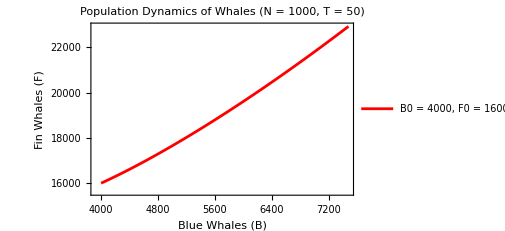
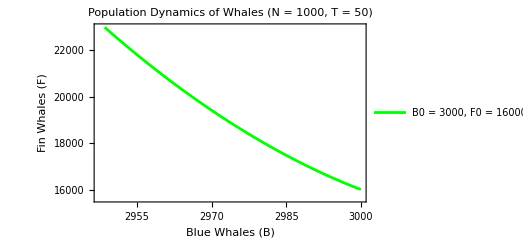
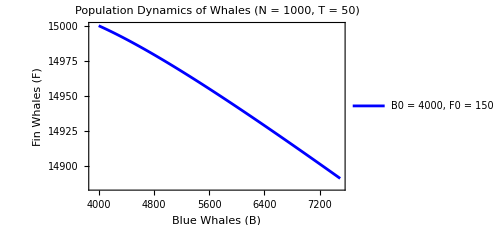
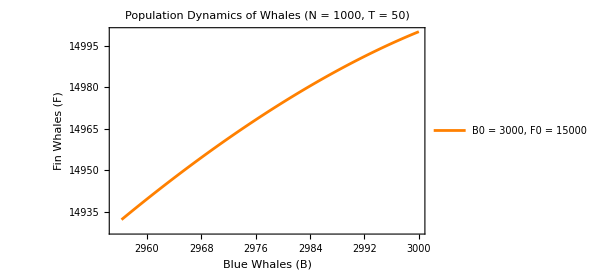

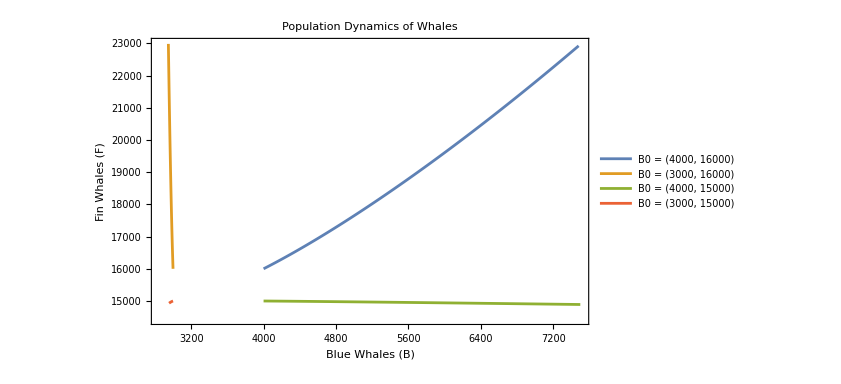

```mathematica
(* Define the system of differential equations *)
dBdt[B_, F_] := 0.05*B*((B - 3000)/(B + 3000))*(1 - B/150000) - 10^-8*B*F
dFdt[B_, F_] := 0.08*F*((F - 15000)/(F + 15000))*(1 - F/400000) - 10^-8*B*F

(* Implement Euler's method *)
eulerMethod[{B0_, F0_}, T_, numSteps_] := Module[{h, tValues, BValues, FValues, dB, dF, B, F},
  h = T/numSteps;
  tValues = Table[t, {t, 0, T, h}];
  BValues = FValues = Table[0, {numSteps + 1}];
  BValues[[1]] = B0;
  FValues[[1]] = F0;
  Do[
   {dB, dF} = {dBdt[B, F], dFdt[B, F]} /. {B -> BValues[[i]], F -> FValues[[i]]};
   BValues[[i + 1]] = BValues[[i]] + h*dB;
   FValues[[i + 1]] = FValues[[i]] + h*dF;
   , {i, 1, numSteps}];
  {tValues, BValues, FValues}
]

(* Define parameters for simulations *)
params = {{{4000, 16000}, {3000, 16000}, {4000, 15000}, {3000, 15000}}, {1000, 50}};

(* Specify colors *)
colors = {Red, Green, Blue, Orange};

(* Perform simulations and plot results *)
plots = Table[
  initialConditions = params[[1, j]];
  {numSteps, T} = params[[2]];
  {tValues, BValues, FValues} = eulerMethod[initialConditions, T, numSteps];
  ListLinePlot[{Transpose[{BValues, FValues}]}, 
   PlotLegends -> {"B0 = " <> ToString[initialConditions[[1]]] <> ", F0 = " <> ToString[initialConditions[[2]]]}, 
   PlotStyle -> colors[[j]], Frame -> True, 
   FrameLabel -> {"Blue Whales (B)", "Fin Whales (F)"}, 
   PlotLabel -> Row[{"Population Dynamics of Whales (N = ", numSteps, ", T = ", T, ")"}]],
  {j, Length[params[[1]]]}]

(* Display the plots *)
Show[plots]

(* Perform simulations and collect results *)
data = Table[
  initialConditions = params[[1, j]];
  {numSteps, T} = params[[2]];
  {tValues, BValues, FValues} = eulerMethod[initialConditions, T, numSteps];
  Transpose[{BValues, FValues}],
  {j, Length[params[[1]]]}]

(* Plot results *)
ListLinePlot[data, PlotLegends -> {"B0 = (4000, 16000)", "B0 = (3000, 16000)", "B0 = (4000, 15000)", "B0 = (3000, 15000)"}, 
 Frame -> True, FrameLabel -> {"Blue Whales (B)", "Fin Whales (F)"}, 
 PlotLabel -> "Population Dynamics of Whales"]
```

From the graph, we can see that 
(4000,16000) both grow back
(3000,16000)  blue whales go extinct,fin whales approach carrying capacity
(4000,15000)  fin whales become extinct, blue whales approach carrying capacity
(3000,15000)   both go extinct